```mathematica
{LabelStyle->18,PlotLabel->"Plot Label",AxesLabel->{"X","Y"}}
raspberryPi=FileNameJoin[{"Z:","RbData","2017-10-28"}];
laptop=FileNameJoin[{"/","home","karl"}];
labComp=FileNameJoin[{"C:","Users","kahrendsen2"}];
dropboxOn=FileNameJoin[{"Dropbox","00School","research","DataRuns"}];
folder=FileNameJoin[{labComp,dropboxOn}];
SetDirectory[folder];
FileNames["*"]
SetOptions[Plot,BaseStyle->{FontSize->24},ImageSize->Large,PlotStyle->{Automatic,20},LabelStyle->27,GridLines->Automatic];
SetOptions[ListPlot,BaseStyle->{FontSize->24},ImageSize->Large,PlotMarkers->{Automatic,20},LabelStyle->27,ImageSize->{960,600},GridLines->Automatic];

plotLabel="Plot Label";
yAxisLabel="Y";
xAxisLabel="X";
ps={LabelStyle->18,PlotLabel->plotLabel,AxesLabel->{xAxisLabel,yAxisLabel}}
```

{LabelStyle→18,PlotLabel→Plot Label,AxesLabel→{X,Y}}

{15-06-09_USBCounterError,15-07-06mockPolarizationData,16-01-14,16-01-21_Data,16-05-25_PolarizationData,16-07-06_PolarizationData,16-08-04_PolarizationData,16-08-07_HeliumTargetPictures,16-08-09_PolarizationData,16-10-17_polarimeter,16-10-27_DataReport,16-11-03_faradayRotation,16-11-07_faradayRotation,16-11-18_faradayRotation,16-12-09_faradayRotation,17-01-31,17-02-17_plusMinus,17-03-06_PlusMinusWavemeter,17-03-10_non-RbFaradayRotation,17-03-15_AimingFor5e12,17-03-15_wavemeterNoRb,17-03-28,17-03-29_pumpLaserFindingCircular,17-03-30_WavemeterReliability,17-04-04_polarization,17-04-06_polarization,17-04-07_wmReliability,17-04-18,17-04-18_polarization,17-04-22,17-04-25_ProbePolarizationDriftOpenChamber,17-04-30_laserReport,17-05-17_DirtyGunRun,17-05-18_ProbeDrift,17-05-19_BetterLaser,17-05-24_SimplifiedPolarization,17-05-25_LaserProfiling,17-06-02,17-06-06_IntensityOfProbeStudy,17-06-11,17-06-13,17-06-16,17-06-17,17-06-25,17-07-01_nRbVsBufferGasAnalysis,17-07-01_PumpLaserAnalysis,17-07-03_lowerNRb_BGPStudy,17-07-03_ProbeDrift,17-07-03_pumpBroadening,17-07-06_lotsOfProbeMeasurements,17-07-06_MagneticField,17-07-06_probePower,17-07-12_polVsPumpPower,17-08-01_rgaInitialScans,17-08-03_redoingSystemDiagnostic,17-08-06_probeDrift,17-08-18_furtherPolarizationStudy,17-08-19_furtherPolarizationStudy2,17-08-22_furtherPolarizationStudyFoundLeak,17-08-29_BvsProbePower_probeDetuneVsMagnetRot,17-09-05_Polarizations_100mTBGP,17-09-20,17-10-03_ElectronGun,17-10-16_ElectronGun,17-10-24_UnpolarizedPolarization,17-10-26_24And30eVRuns,17-10-28_24and30eVRedux,17-11-04_MoreUnpolarizedRuns,17-11-06_UnpolarizedRuns2,17-11-15_BalancedPhotoDetector,17-11-18_SystemDiagnosis,17-12-18_SystemDiagnosis,17-12-20_PolarizingElectrons,18-01-03_PolarizingElectrons,18-01-04_PolarizingElectrons,18-01-10_ChamberWarming,18-01-11_SystemDiagnostics,18-01-12_recreatingPolFigure,18-01-13_recreatingPolFigureIncreasedT,18-01-16_morePolarization,18-01-20_electronPolarization,18-01-25_excitationFunctions,18-01-28_bufferGasPressureVsCounts,18-01-28_exFnCurrentNormalized.png,18-01-28_exFnMolyCounts.png,18-01-28_exFnRawCounts.png,18-01-28_exFnSignalCounts.png,18-01-28_hayesReproduction,18-02-12_polarizedElectrons,18-02-13,18-02-15_addtlBGP,dataDump,pumpQWP,test.png,wavemeterOffsets}

{LabelStyle→18,PlotLabel→Plot Label,AxesLabel→{X,Y}}

```mathematica
SetDirectory[FileNameJoin[{folder,"18-02-13","data"}]];
files=FileNames["EX*.dat"]
```

{EX2018-02-13_013554.dat,EX2018-02-13_014854.dat,EX2018-02-13_023109.dat,EX2018-02-13_023357.dat,EX2018-02-13_050758.dat,EX2018-02-13_170321.dat,EX2018-02-13_173556.dat,EX2018-02-13_174047.dat,EX2018-02-13_182224.dat,EX2018-02-13_230939.dat,EX2018-02-13_233300.dat,EX2018-02-14_042016.dat,EX2018-02-14_044342.dat,EX2018-02-14_093056.dat,EX2018-02-14_113518.dat,EX2018-02-14_120100.dat,EX2018-02-14_131606.dat,EX2018-02-14_141849.dat,EX2018-02-14_162159.dat,EX2018-02-14_192323.dat,EX2018-02-14_203423.dat,EX2018-02-14_233539.dat}

## Performs Gaussian Analysis of Excitation Function (both with counts and current)

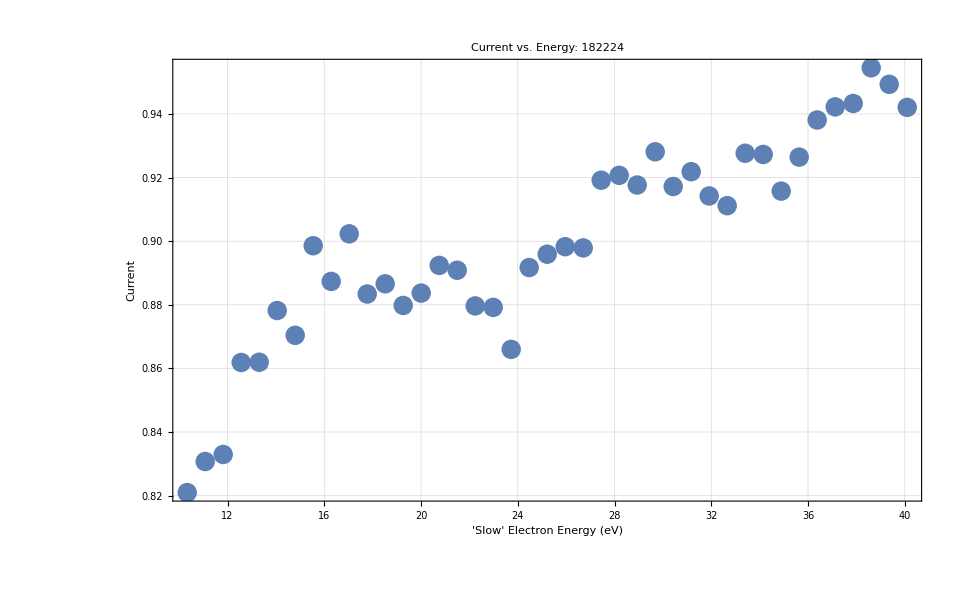

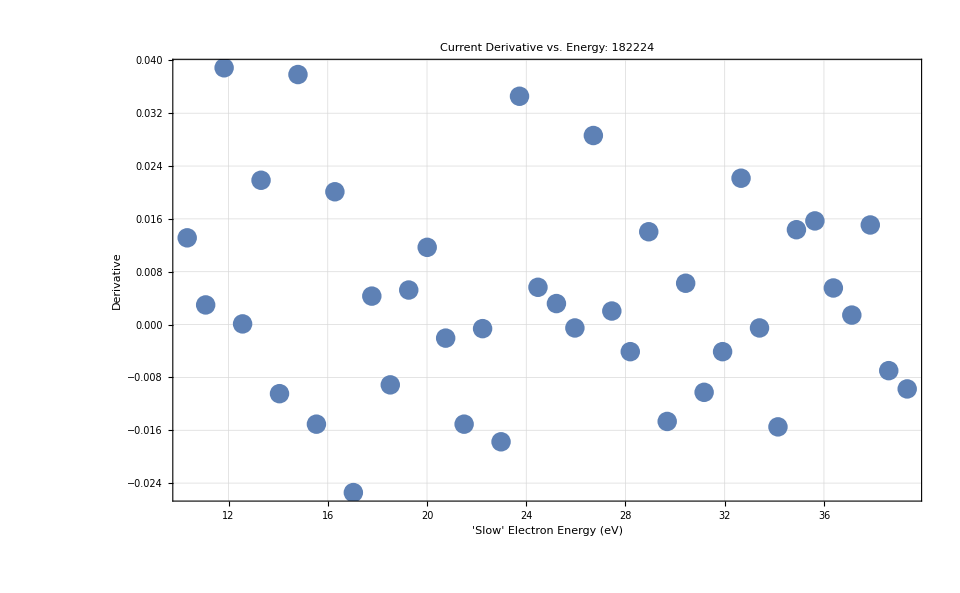

7.83228

15.1677

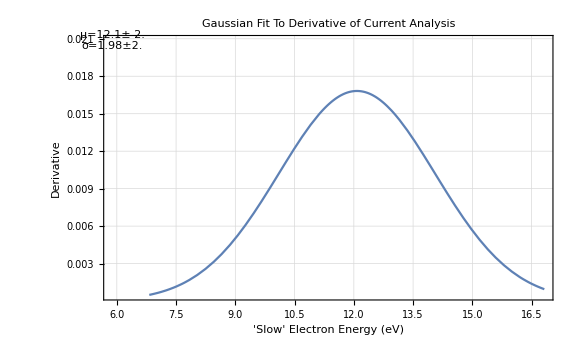

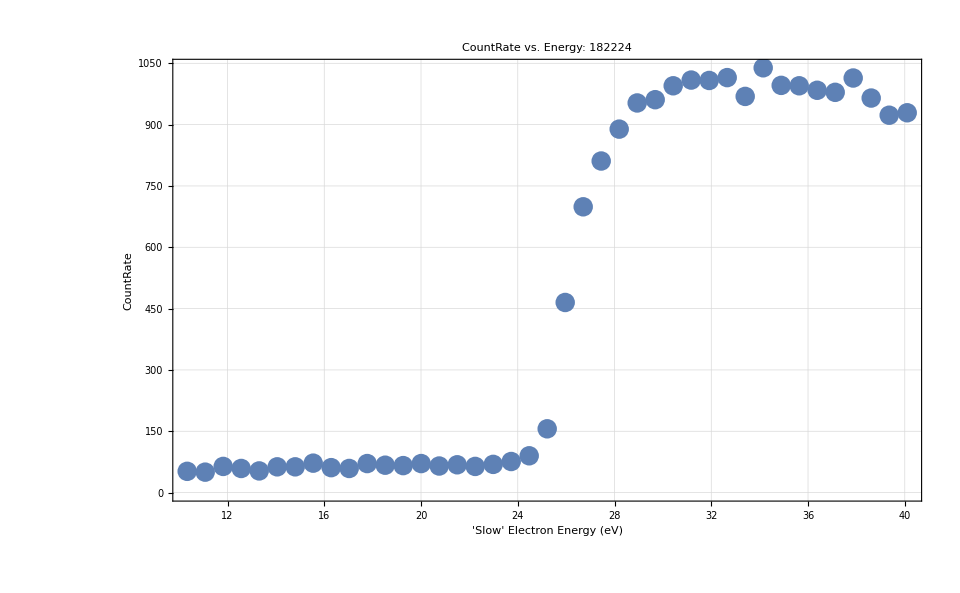

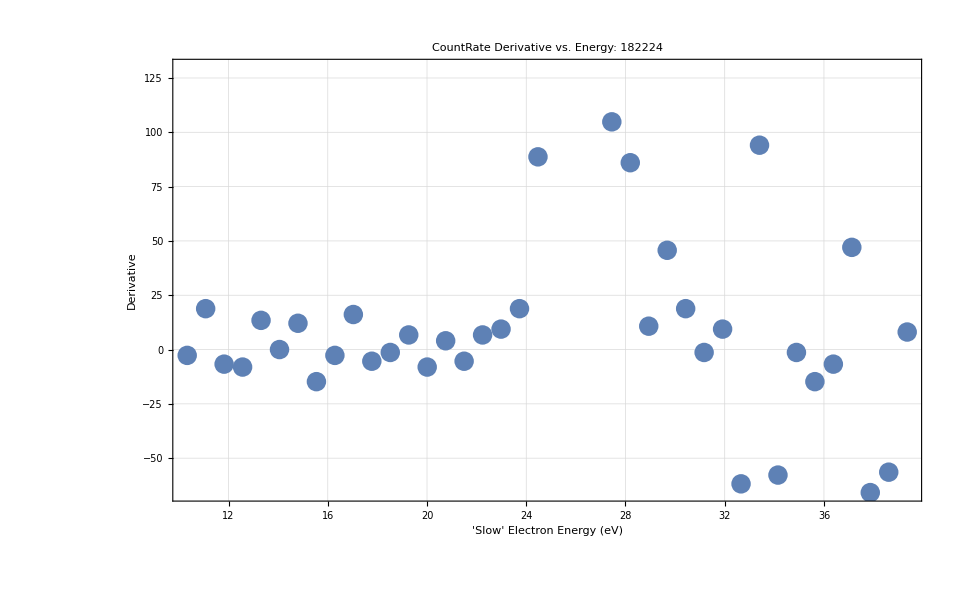

23.939

-0.939043

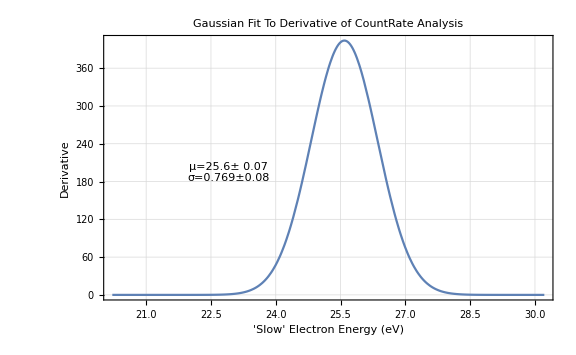

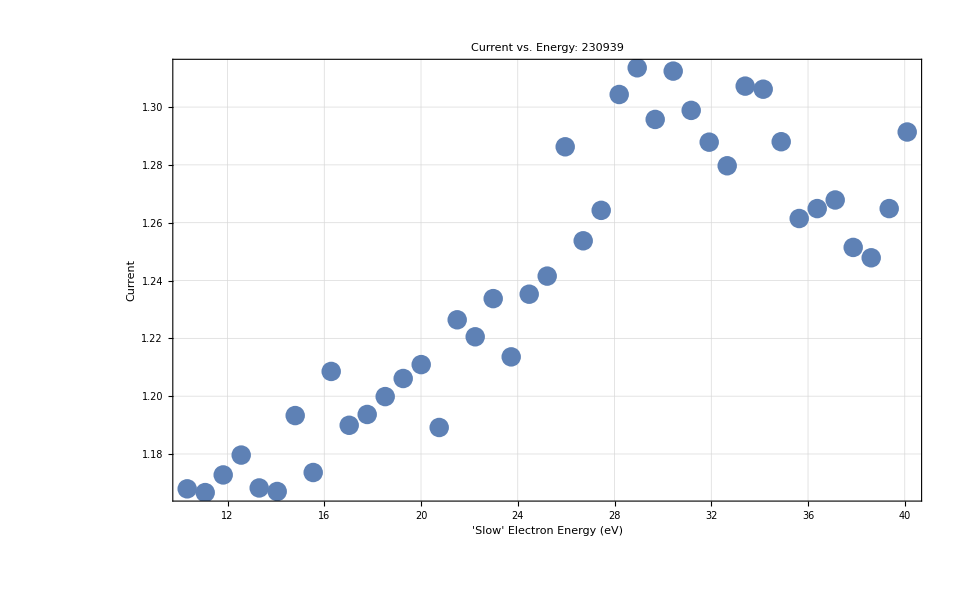

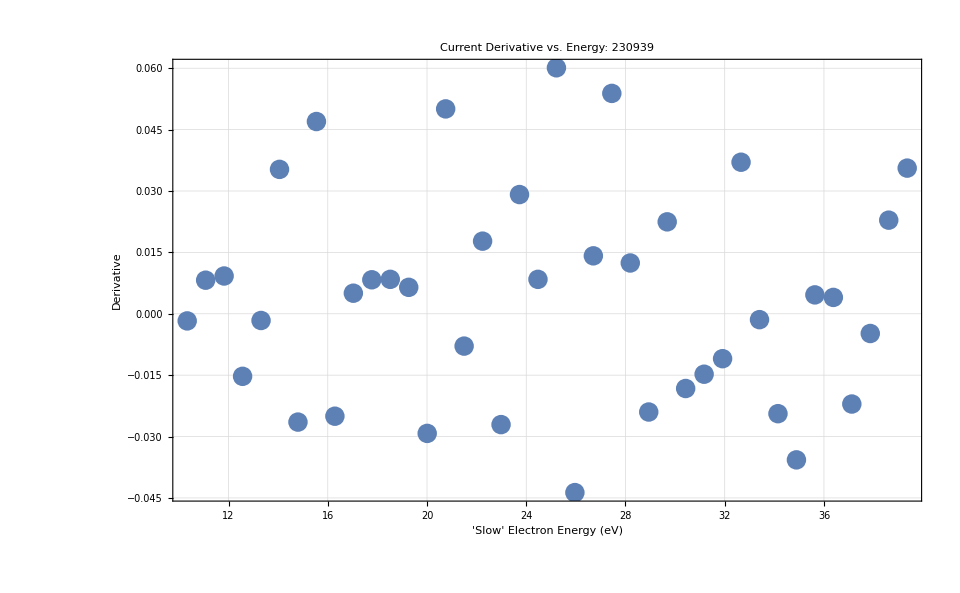

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

24.5698

-1.56979

NumberForm::reqsigz: Requested number precision is lower than number of digits shown; padding with zeros.

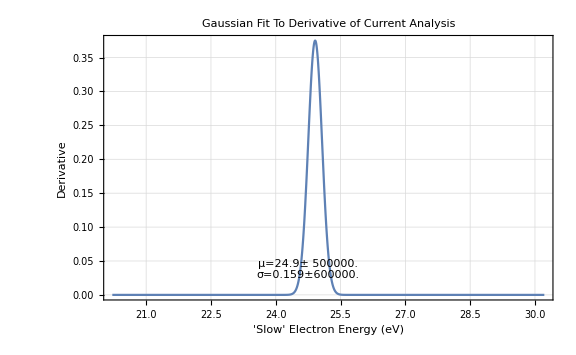

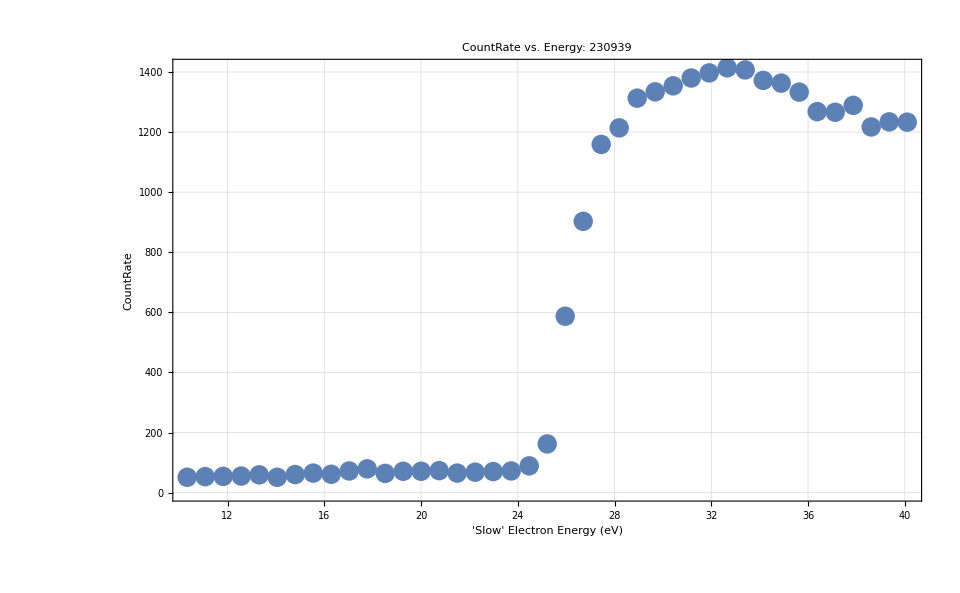

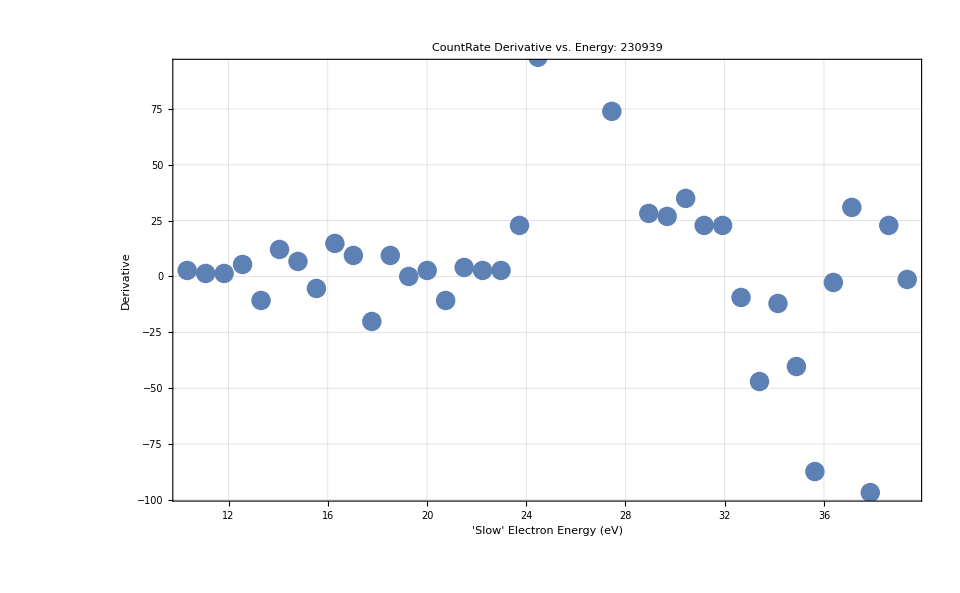

23.844

-0.844004

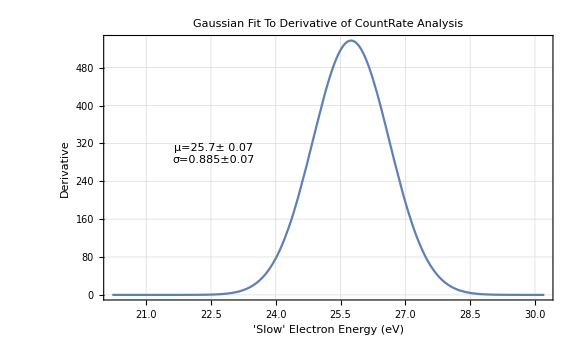

```mathematica
ExcitationFunctionProcessor["182224"]
ExcitationFunctionProcessor["230939"]
```

## Prints out the comments from all of the file names.

```mathematica
For[i=1,i≤Length[files],i++,
comments=GetFileHeaderInfo[files[[i]]]["#Comments:"];
Print[comments];
];
```

1

getting excitation function to set scale for extended run

Run 1,

Run 2,

Run ,

Run 1, Recreating Hayes data, room lights on. Moly Counts

Run 2, Recreating Hayes data, room lights on. Moly Counts

Run 3, Recreating Hayes data, room lights on. Moly Counts

Run 4, Recreating Hayes data, room lights on. Moly Counts

Run 1, Recreating Hayes data, room lights on. dark Counts

## Shows Graphs for the normalization process of the excitation function

{115.054,114.146,114.214,113.764,113.352,113.756,112.924,112.917,112.016,111.833,111.81,111.199,111.703,110.688,110.352,109.825,109.283,109.581,108.688,108.917,108.245,108.138,107.963,107.261,107.635,106.833,106.894}

{7.41391,7.81457,7.24077,7.68257,7.45467,8.1402,7.20836,7.66936,7.81138,7.48438,7.73634,7.47307,7.57365,7.54373,7.34921,7.43909,6.90864,6.48835,5.55719,3.81024,2.14328,1.33163,1.01887,0.978924,0.724673,0.664587,0.514527}

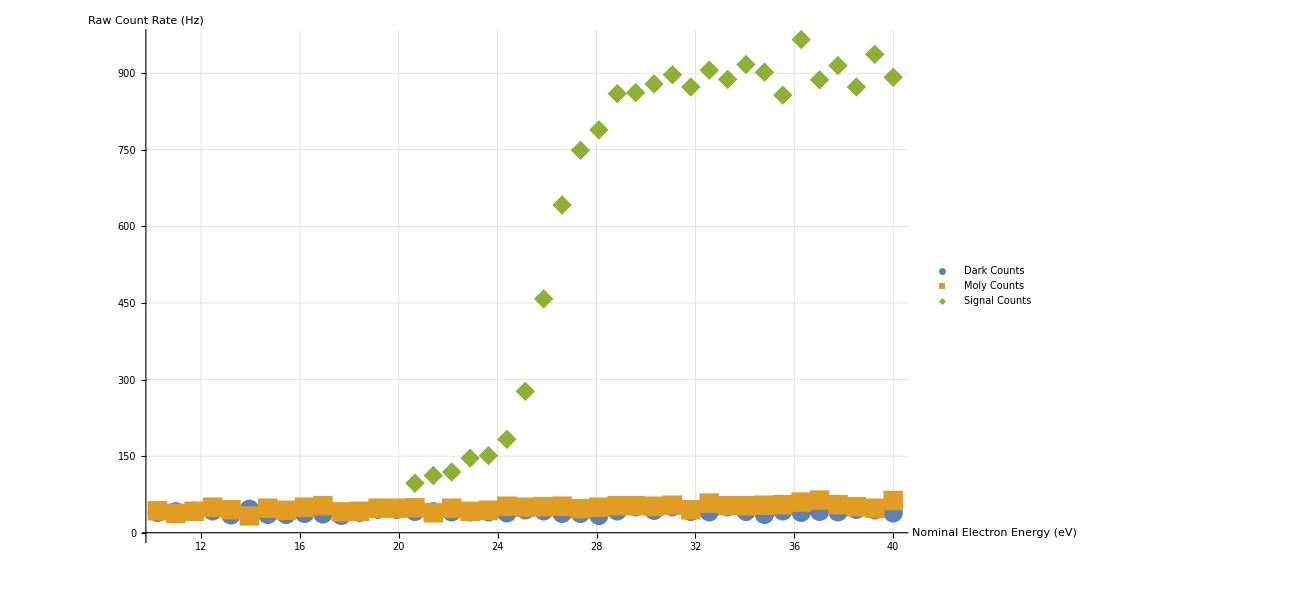

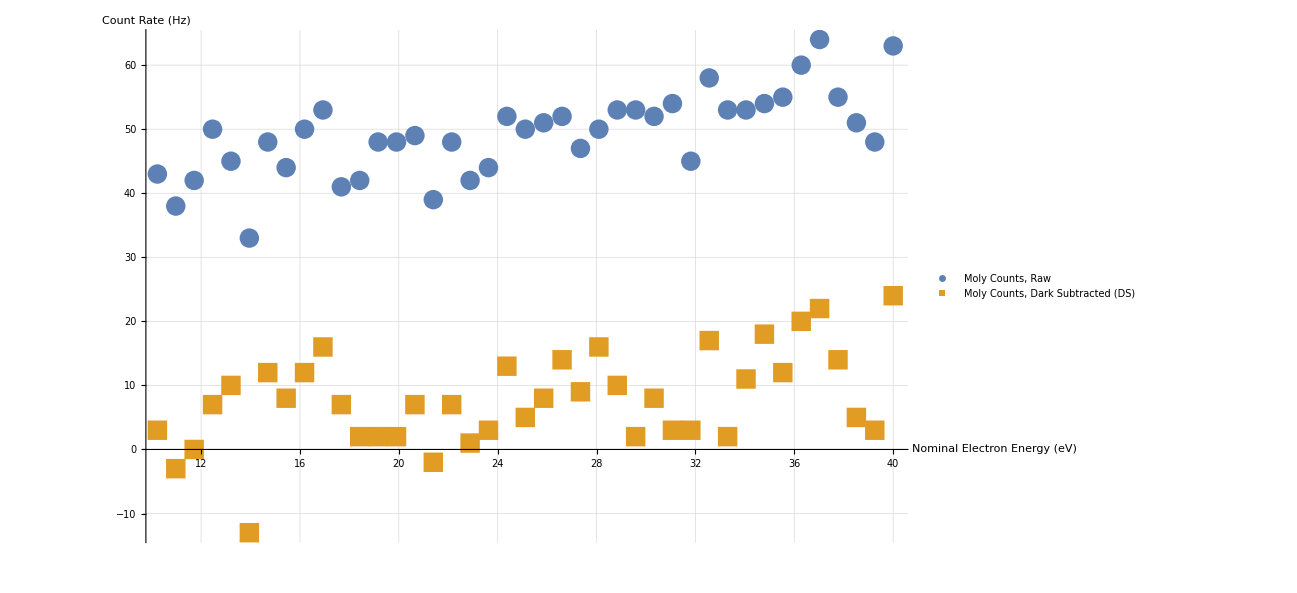

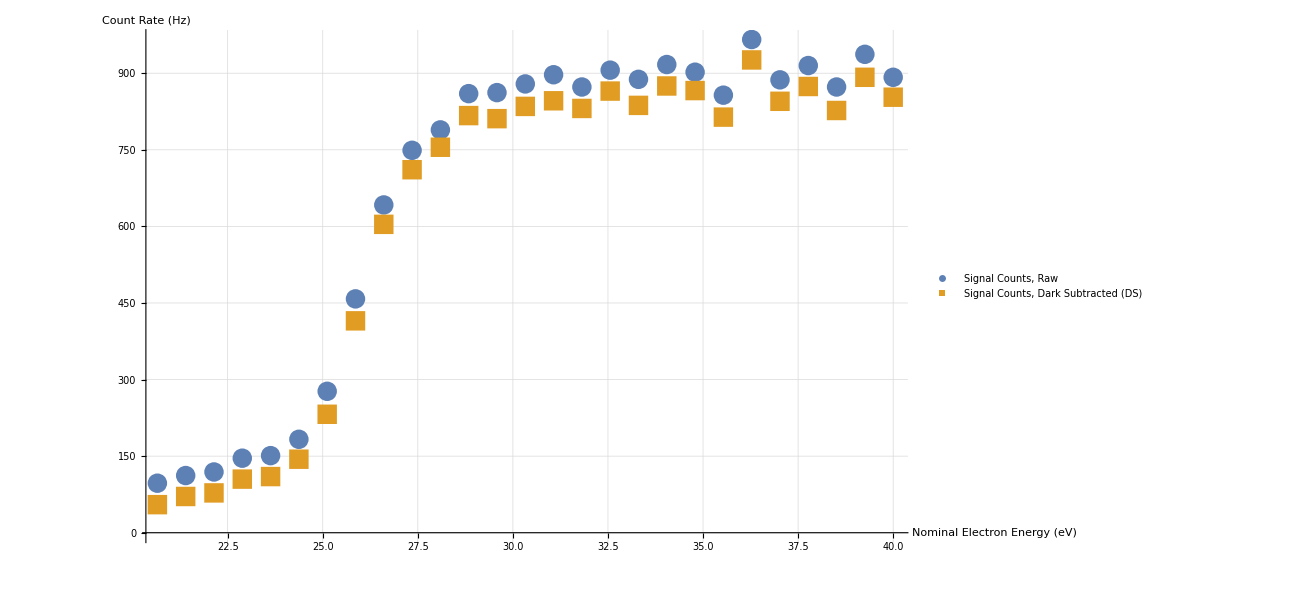

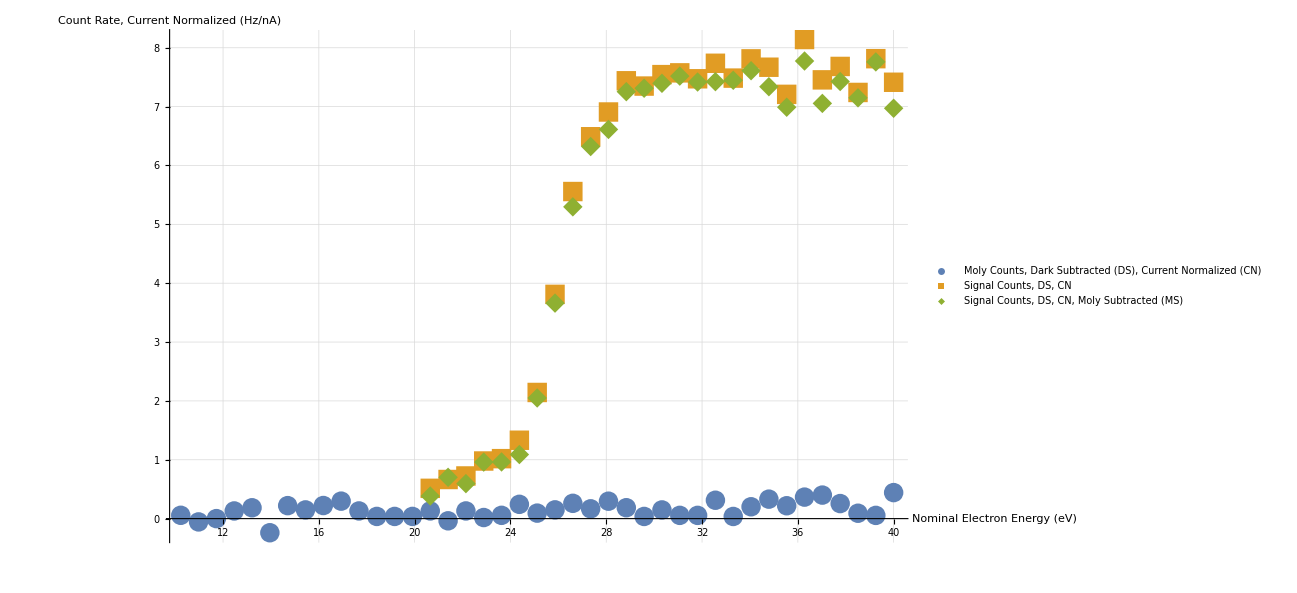

0.143924

0.135327

{{40.,6.63982},{39.2558,7.39017},{38.5117,6.80888},{37.7675,7.07311},{37.0233,6.71892},{36.2792,7.40454},{35.535,6.65684},{34.7909,6.98913},{34.0467,7.24764},{33.3025,7.09308},{32.5584,7.07054},{31.8142,7.06472},{31.07,7.16035},{30.3259,7.04398},{29.5817,6.96409},{28.8376,6.90847},{28.0934,6.29766},{27.3492,6.02079},{26.6051,5.04504},{25.8609,3.48708},{25.1167,1.95217},{24.3726,1.03693},{23.6284,0.917106},{22.8842,0.914571},{22.1401,0.565928},{21.3959,0.668457},{20.6518,0.365506}}

24.9929

-1.99292

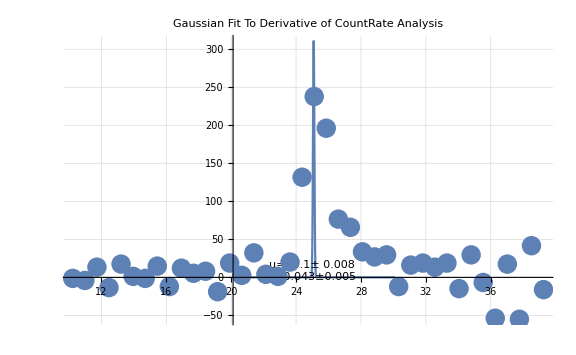

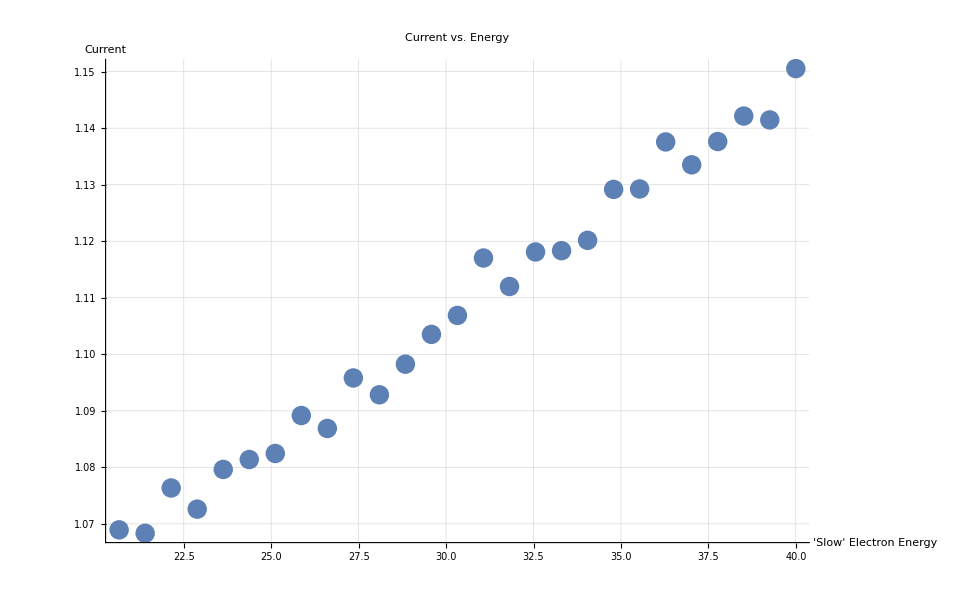

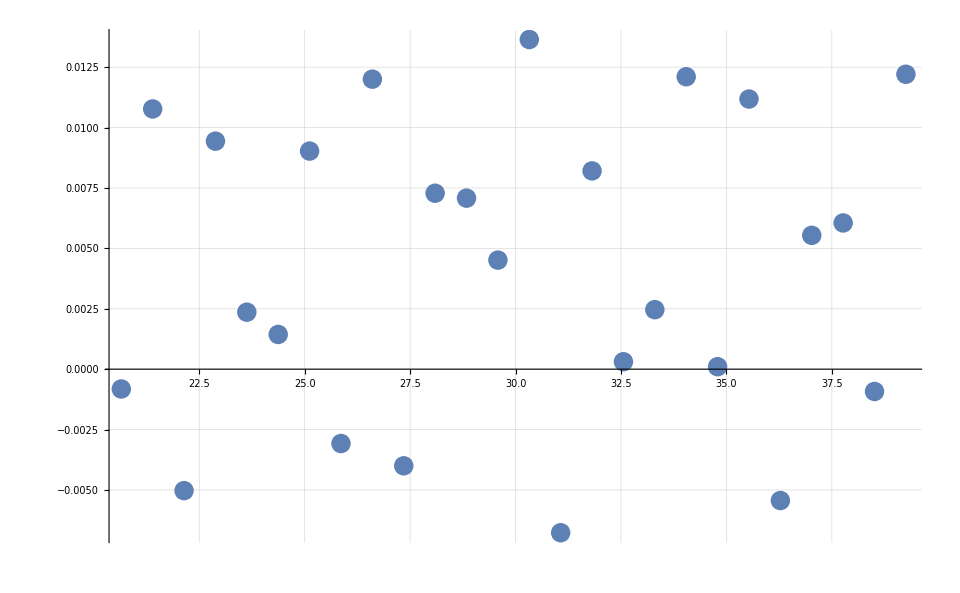

-17.378

40.378

NumberForm::reqsigz: Requested number precision is lower than number of digits shown; padding with zeros.

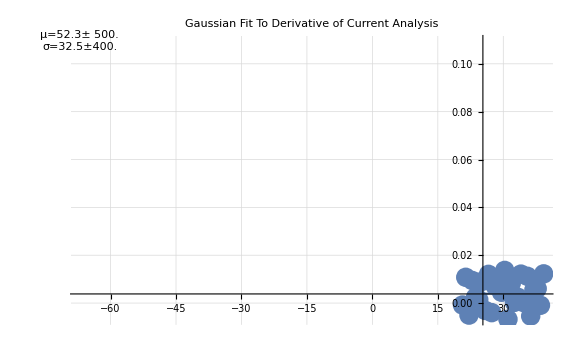

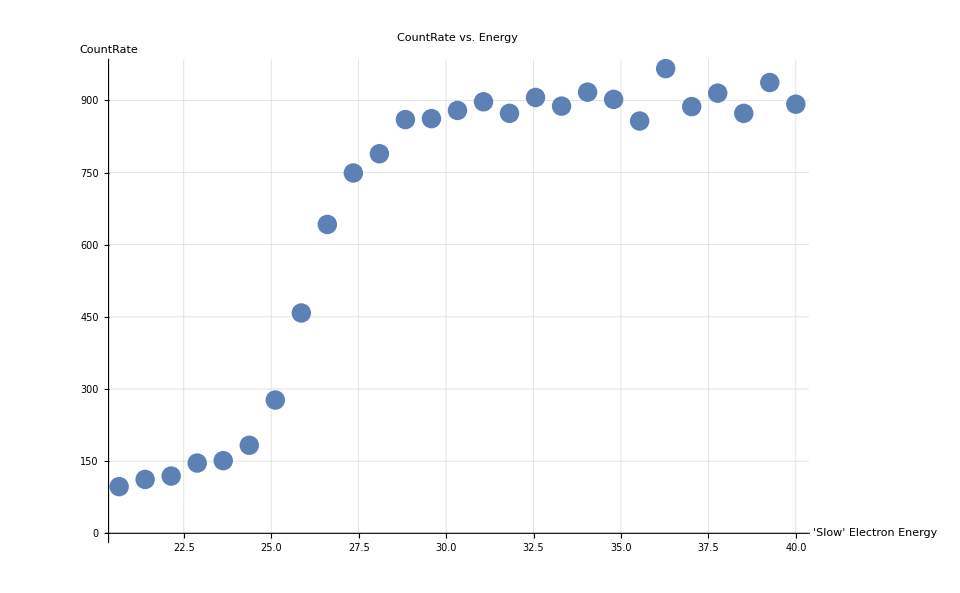

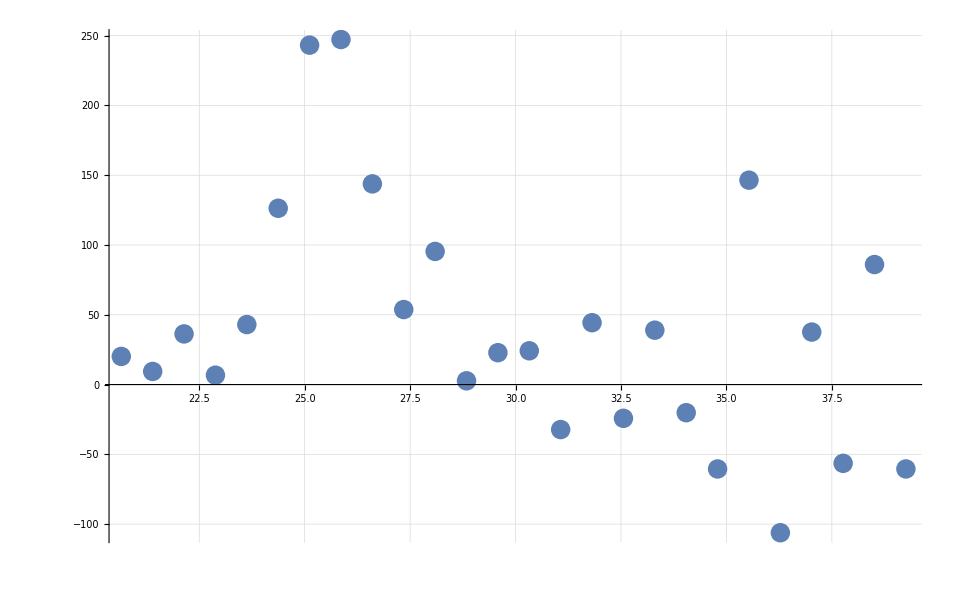

23.2221

-0.222091

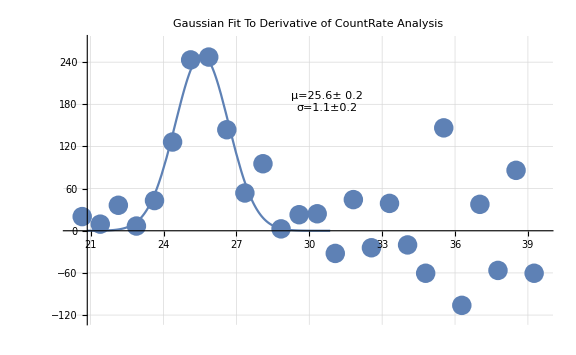

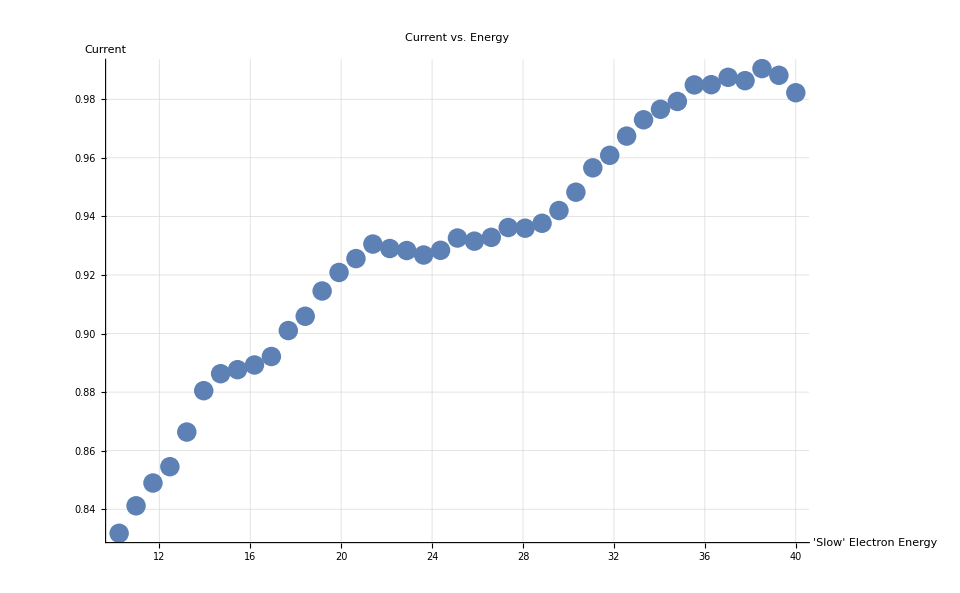

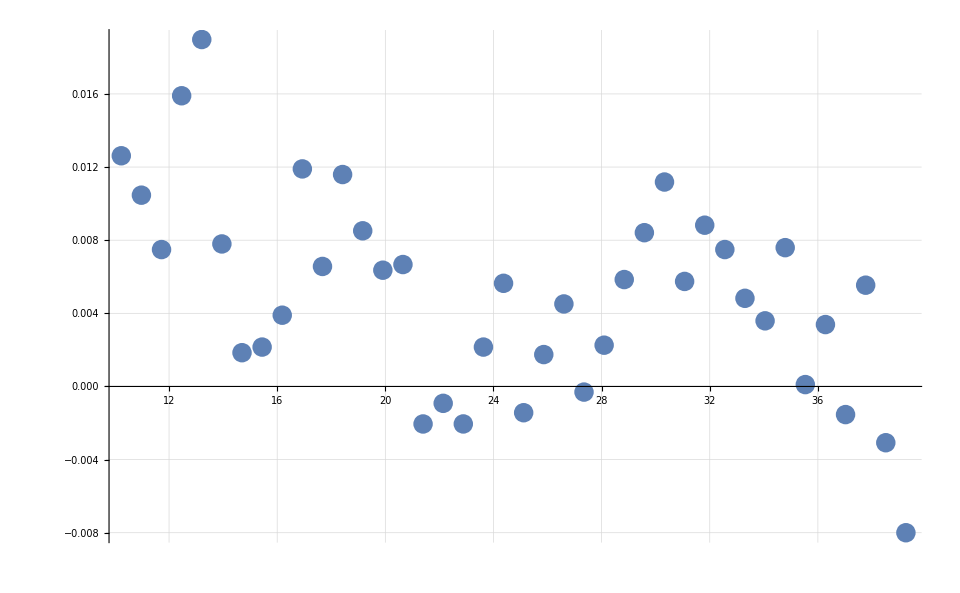

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

-367.817

390.817

NumberForm::reqsigz: Requested number precision is lower than number of digits shown; padding with zeros.

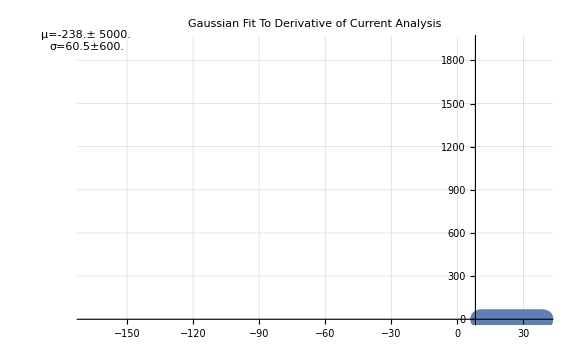

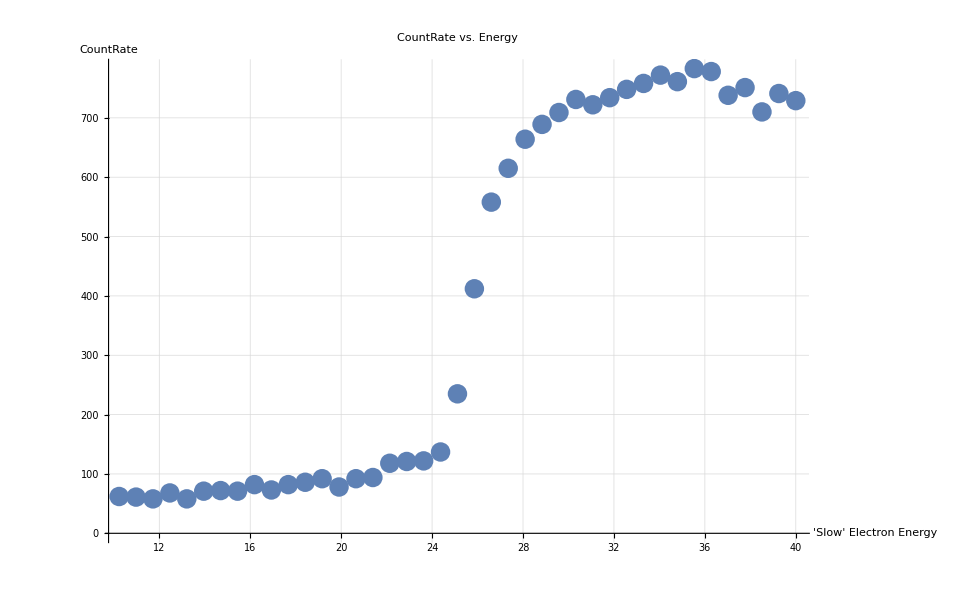

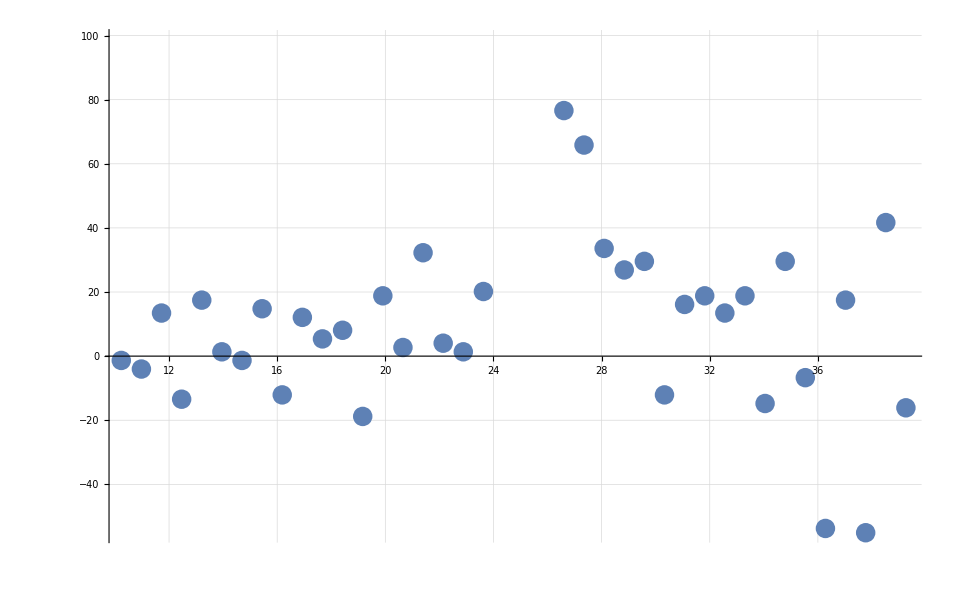

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

24.9929

-1.99292

-Graphics-

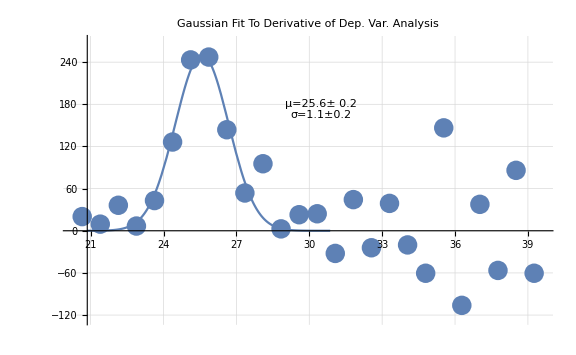

-Graphics-

-Graphics-

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

-367.817

390.817

NumberForm::reqsigz: Requested number precision is lower than number of digits shown; padding with zeros.

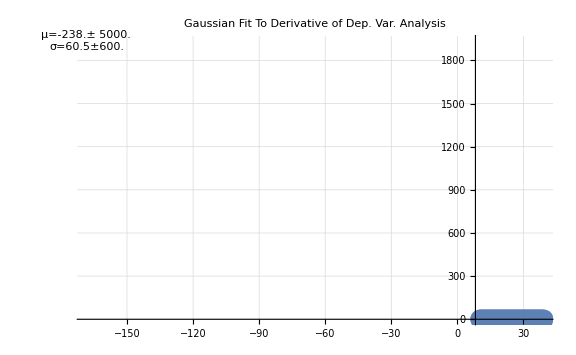

-Graphics-

-Graphics-

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

24.9929

-1.99292

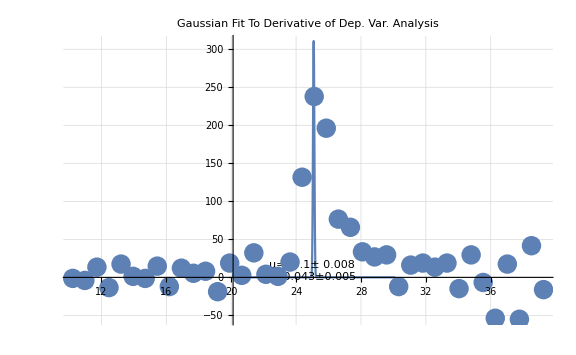

```mathematica
dataFolderDate="18-01-28";
darkTimeStamp="014911";
darkData=GetFileDataset[files[[GetIndexOfFilenameFromTimestamp[files,darkTimeStamp]]]];
darkHeader=GetFileHeaderInfo[files[[GetIndexOfFilenameFromTimestamp[files,darkTimeStamp]]]];

molyTimeStamp="191413";
molyData=GetFileDataset[files[[GetIndexOfFilenameFromTimestamp[files,molyTimeStamp]]]];
molyHeader=GetFileHeaderInfo[files[[GetIndexOfFilenameFromTimestamp[files,molyTimeStamp]]]];

signalTimeStamp="183912";
signalData=GetFileDataset[files[[GetIndexOfFilenameFromTimestamp[files,signalTimeStamp]]]];
signalHeader=GetFileHeaderInfo[files[[GetIndexOfFilenameFromTimestamp[files,signalTimeStamp]]]];

energyOffset=0;
nA=1*10^-9;
torrTomTorr=1000;
darkCounts=Normal[darkData[All,{"SecondaryElectronEnergy","CountRate","Current"}][All,Values]];
energyArray=Transpose[darkCounts][[1]]+energyOffset;
darkCountArray=Transpose[darkCounts][[2]];

molyCounts=Normal[molyData[All,{"SecondaryElectronEnergy","CountRate","Current"}][All,Values]];
molyCountArray=Transpose[molyCounts][[2]];
molyCurrentMag=molyHeader["#MagnitudeOfCurrent(*10^-X):"];
molyCurrentArrayNa=Transpose[molyCounts][[3]]*10^(-molyCurrentMag)/nA;
ListPlot[{Transpose[{energyArray,darkCountArray}],Transpose[{energyArray,molyCountArray}]}];
molyDarkSubtracted=molyCountArray-darkCountArray;
molyCurrentNorm=molyDarkSubtracted/molyCurrentArrayNa;

signalCounts=Normal[signalData[All,{"SecondaryElectronEnergy","CountRate","Current"}][All,Values]];
signalCountArray=Transpose[signalCounts][[2]];
signalEnergyArray=Transpose[signalCounts][[1]]+energyOffset;
signalCurrentMag=signalHeader["#MagnitudeOfCurrent(*10^-X):"];
signalCurrentArrayNa=Transpose[signalCounts][[3]]*10^(-signalCurrentMag)/nA
signalDarkSubtracted=signalCountArray-Take[darkCountArray,{1,Length[signalCountArray]}];
signalCurrentNorm=signalDarkSubtracted/signalCurrentArrayNa
signalMolySubtracted=signalCurrentNorm-Take[molyCurrentNorm,{1,Length[signalCountArray]}];
signalHeNorm=signalMolySubtracted/(signalHeader["#CVGauge(He)(Torr):"]*torrTomTorr);

xAxisLabel="Nominal Electron\nEnergy (eV)";
yAxisLabel="Raw Count Rate (Hz)";
rawCountsPlot=ListPlot[{Legended[Drop[darkCounts,None,{-1}],"Dark Counts"],Legended[Drop[molyCounts,None,{-1}],"Moly Counts"],Legended[Drop[signalCounts,None,{-1}],"Signal Counts"]},AxesLabel->{xAxisLabel,yAxisLabel},GridLines->Automatic]

yAxisLabel="Count Rate (Hz)";
molyCountsPlot=ListPlot[{Legended[Transpose[{energyArray,molyCountArray}],"Moly Counts, Raw"],Legended[Transpose[{energyArray,darkSubtractedMoly}],"Moly Counts, Dark Subtracted (DS)"]},AxesLabel->{xAxisLabel,yAxisLabel}]

yAxisLabel="Count Rate (Hz)";
signalCountsPlot=ListPlot[{Legended[Transpose[{Take[energyArray,{1,Length[signalMolySubtracted]}],signalCountArray}],"Signal Counts, Raw"],Legended[Transpose[{Take[energyArray,{1,Length[signalMolySubtracted]}],signalDarkSubtracted}],"Signal Counts, Dark Subtracted (DS)"]},AxesLabel->{xAxisLabel,yAxisLabel}]

yAxisLabel="Count Rate,\nCurrent Normalized (Hz/nA)";
currentNormalizedPlot=ListPlot[{Legended[Transpose[{energyArray,currentNormMoly}],"Moly Counts, Dark Subtracted (DS),\nCurrent Normalized (CN)"],Legended[Transpose[{Take[energyArray,{1,Length[signalMolySubtracted]}],signalCurrentNorm}],"Signal Counts, DS, CN"],
Legended[Transpose[{Take[energyArray,{1,Length[signalMolySubtracted]}],signalMolySubtracted}],"Signal Counts, DS, CN, Moly Subtracted (MS)"]
},AxesLabel->{xAxisLabel,yAxisLabel}]

Mean[molyCurrentNorm]
StandardDeviation[molyCurrentNorm]

fullyNormalizedExcitationFunction=Transpose[{Take[energyArray,{1,Length[signalMolySubtracted]}],signalHeNorm}]

Export[dataFolderDate<>"_exFnRawCounts.png",rawCountsPlot,ImageResolution->200];
Export[dataFolderDate<>"_exFnMolyCounts.png",molyCountsPlot,ImageResolution->200];
Export[dataFolderDate<>"_exFnSignalCounts.png",signalCountsPlot,ImageResolution->200];
Export[dataFolderDate<>"_exFnCurrentNormalized.png",currentNormalizedPlot,ImageResolution->200];
```

```mathematica
GetFileHeaderInfo[dataFileName_]:=Module[{rawFile,data,association,k,rawImport,removedNulls,joinedWithSpaces},
rawFile=Import[dataFileName];
data={};
association=Association[];
k=1;
While[StringPart[rawFile[[k]][[1]],1]=="#",
If[Length[rawFile[[k]]]> 2,
rawImport=Take[rawFile[[k]],{2,-1}];
removedNulls=DeleteCases[rawImport,Null];
joinedWithSpaces=StringRiffle[removedNulls];
association=Append[association,rawFile[[k]][[1]]->joinedWithSpaces];
,
association=Append[association,rawFile[[k]][[1]]->rawFile[[k]][[2]]];
];
k++;
];
association
];
GetFileDataset[dataFileName_]:=Module[{rawFile,headerStrippedData,columnHeaderLineNumber,lastColumnToImport,j,k,ass,tabularData,ds,rbAbsorptionRef,rbAbsorptionPro},
rawFile=Import[dataFileName];
k=1;

While[StringPart[rawFile[[k]][[1]],1]=="#",
k++;
];


headerStrippedData=Take[rawFile,{k,-1},All];
tabularData={};
For[j=2,j≤Length[headerStrippedData],j++,
If[Length[headerStrippedData[[j]]]>1,
ass=Association[];
For[k=1,k≤Length[headerStrippedData[[j]]],k++,
ass=Append[ass,headerStrippedData[[1]][[k]]->headerStrippedData[[j]][[k]]];
];
tabularData=Append[tabularData,ass];
]
];
ds =Dataset[tabularData]
];

GaussianAnalyzer[timeString_,dependentVariableString_]:=Module[{fitInfo, bothPlot, derivativePlot,entry,file,ps,header,data,energy,energyDiff,depVar,depVarDiff,energyOneRemoved,depVarDer,plotTitle,plotData,plotData2,fit,model,pe,errors,gaussModel,m,σ,x,ampl,maxDerPos,energyOfPeak,dataLabel1,dataLabel2,x1,y1,offset, new23},
file=FileNames["*"<>ToString[timeString]<>".dat"][[1]];

header=GetFileHeaderInfo[file];
data=GetFileDataset[file];
energy=Reverse[Normal[data[All,"SecondaryElectronEnergy"]]];
depVar=Reverse[Normal[data[All,dependentVariableString]]];
depVarDiff=Differences[depVar];
energyDiff=Differences[energy];
energyOneRemoved=Take[energy,{1,-2}];
depVarDer=depVarDiff/energyDiff;
Print[ListPlot[Transpose[{energy,depVar}],PlotLabel->dependentVariableString<>" vs. Energy: "<>timeString,FrameLabel->{"'Slow' Electron Energy (eV)",dependentVariableString},Frame->True]];
Print[ListPlot[Transpose[{energyOneRemoved,depVarDer}],PlotLabel->dependentVariableString<>" Derivative\nvs. Energy: "<>timeString,FrameLabel->{"'Slow' Electron Energy (eV)","Derivative"},Frame->True]];


plotTitle="Gaussian Analysis";

plotData=Transpose[{energy,depVar}];
plotData2=Transpose[{energyOneRemoved,depVarDer}];


(*
yAxisTitle="d(Counts)/d(Energy)";
xAxisTitle="Electron Energy (eV)";
*)
dataLabel1="Data";
dataLabel2="Derivative";

ps={ImageSize->Large, PlotLabel->plotTitle,AxesLabel->{"X","Y"}};

plotData=plotData2;
gaussModel[x_]=ampl Evaluate[PDF[NormalDistribution[m,σ],x]];
(*Find the position of the peak of the derivative data*)
maxDerPos=Position[depVarDer,Max[depVarDer]][[1]];
energyOfPeak=energyOneRemoved[[maxDerPos]][[1]];

fit=NonlinearModelFit[plotData,gaussModel[x],{ampl,{m,energyOfPeak},{σ,.9}},x];
model=Normal[fit];
pe=fit["BestFitParameters"]; (*Parameter Estimates*)
errors=fit["ParameterErrors"];

new23=m-(2*Sqrt[2Log[10]]σ)/2/.pe;
offset=23-new23;


Print[new23];
Print[offset];


x1=energyOfPeak-(3σ/.pe);
y1=.25*(ampl)/.pe;
fitInfo=StringForm["μ=``± ``\nσ=``±``",NumberForm[m/.pe,3],NumberForm[errors[[2]],1],NumberForm[σ/.pe,3],NumberForm[errors[[3]],1]];
Print[Show[{Plot[gaussModel[x]/.pe,{x,energyOfPeak-5,energyOfPeak+5},PlotRange->All,PlotLabel->"Gaussian Fit To Derivative\nof "<>dependentVariableString<>" Analysis",Frame->True,FrameLabel->{"'Slow' Electron Energy (eV)","Derivative"}],
Graphics[Text[fitInfo,{x1,y1}],BaseStyle->15]}]];
bothPlot=ListPlot[{Legended[plotData,dataLabel2],Legended[plotData2,dataLabel1]}];
derivativePlot=ListPlot[Legended[plotData2,dataLabel2],ps];

entry ={header["#Filename:"],header["#CVGauge(N2)(Torr):"],data[1,"N2Offset"],data[1,"bias"],m/.pe, σ/.pe,depVar[[1]],depVar[[-1]]}
];

ExcitationFunctionProcessor[timeString_]:=Module[{file,ps,header,data,energy,energyDiff,current,currentDiff,energyOneRemoved,currentDer,plotTitle,plotData,plotData2,fit,model,pe,errors,gaussModel,m,σ,x,ampl,maxDerPos,energyOfPeak,x1,y1},
GaussianAnalyzer[timeString,"Current"];
GaussianAnalyzer[timeString,"CountRate"];
];

GetIndexOfFilenameFromTimestamp[files_,timestamp_]:=Module[{i,index},
For[i=1,i≤Length[files],i++,
If[StringContainsQ[ files[[i]],timestamp],index=i]
];
index
];

SubtractDark[darkDataset_,molyDataset_]:=Module[{},
];

ExcitationFunctionBackgroundSubtractor[darkExcitation,molyExcitation,signalExcitation];
```